```mathematica
pv1={1,(-1+Sqrt[5])/4,(-1-Sqrt[5])/4,(-1-Sqrt[5])/4};
pv2={0,Sqrt[(5+Sqrt[5])/8],Sqrt[(5-Sqrt[5])/8],-Sqrt[(5-Sqrt[5])/8]};
pv3={1,(-1-Sqrt[5])/4,(-1+Sqrt[5])/4,(-1+Sqrt[5])/4};
pv4={0,Sqrt[(5-Sqrt[5])/8],-Sqrt[(5+Sqrt[5])/8],Sqrt[(5+Sqrt[5])/8]};
```

```mathematica
vecOrth[v_]:={v.pv3,v.pv4};
```

```mathematica
badvecs={{2,1,0,0},{1,2,0,0},{1,-1,-1,-1},{-1,-2,-2,-2},{0,2,1,0},{0,1,2,0},{0,0,2,1}};
```

```mathematica
badproj=ToRadicals[FullSimplify[Map[vecOrth,badvecs]]]
```

{{1/4 (7-√5),1/2 √(1/2 (5-√5))},{1/2 (1-√5),√(1/2 (5-√5))},{1/4 (7-√5),-1/2 √(1/2 (5-√5))},{1/2 (1-√5),-√(1/2 (5-√5))},{1/4 (-3-√5),1/4 √(50-22 √5)},{1/4 (-3+√5),-1/4 √(50-10 √5)},{3/4 (-1+√5),-1/2 √(1/2 (5+√5))}}

```mathematica
IDR=(GoldenRatio+1)/2;
ODR=GoldenRatio^2/Sqrt[GoldenRatio^2+1];
DecVertAlt={{IDR,Sqrt[(GoldenRatio+1)/(GoldenRatio+2)]/2},{GoldenRatio/2,Sqrt[(8*GoldenRatio+5)/(GoldenRatio+2)]/2},{0,ODR},{-GoldenRatio/2,Sqrt[(8*GoldenRatio+5)/(GoldenRatio+2)]/2},{-IDR,Sqrt[(GoldenRatio+1)/(GoldenRatio+2)]/2},{-IDR,-Sqrt[(GoldenRatio+1)/(GoldenRatio+2)]/2},{-GoldenRatio/2,-Sqrt[(8*GoldenRatio+5)/(GoldenRatio+2)]/2},{0,-ODR},{GoldenRatio/2,-Sqrt[(8*GoldenRatio+5)/(GoldenRatio+2)]/2},{IDR,-Sqrt[(GoldenRatio+1)/(GoldenRatio+2)]/2}};
```

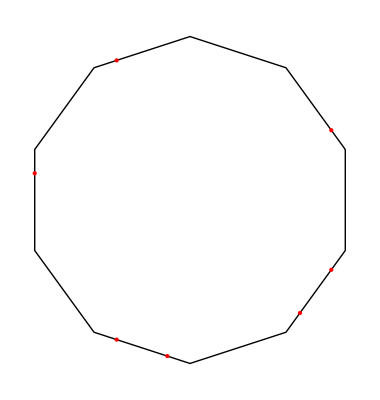

```mathematica
Show[Graphics[Line[Append[DecVertAlt,DecVertAlt[[1]]]]],
Graphics[{PointSize[Large],Red,Point[badproj]}]]
```